```mathematica
bucket={};
rangeStrength={};
ratioStrength={};
$tick;
Clear[δ];
Do[
(* linear system *)
Clear[basis];
basis[θ_]:=Table[Cos[k θ],{k,0,δ}];
(* build linear system *)
A=BuildAFourierCos[mesh,δ];
(* least squares solution *)
x=LeastSquares[A,b];
(* error analysis *)
error[A//N,x,b];
rmax=Max[residual];
rmin=Min[residual];
residualRange=rmax-rmin;
bucket=AppendTo[bucket,{δ,1-residualRange/brange,rmax,rmin}];
rangeStrength=AppendTo[rangeStrength,{δ,1-residualRange/brange}];
ratioStrength=AppendTo[ratioStrength,{δ,totalError/(b.b)}];
,{δ,0,50}];
tiempo["full sweep"]
```

full sweep
CPU time: 16.476 sec
elapsed time: 2.808222 sec

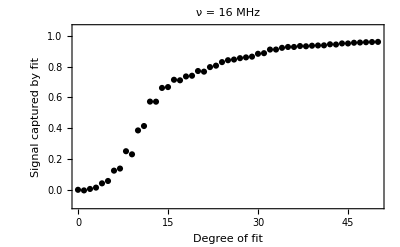

```mathematica
g003=ListPlot[rangeStrength,
ipad,
Frame->True,
PlotStyle->Black,
PlotRange->{Automatic,{-0.1,1.05}},
PlotLabel->"ν = "<>ToString[nu]<>" MHz",
FrameLabel->{"Degree of fit","Signal captured by fit"}
]
```

```mathematica
Export[dirData<>"strength.csv",bucket]
```

/Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/fourier/worst/data/strength.csv

```mathematica
multiExport["agg-signal-captured",g003]
```